```mathematica
ClearAll["`*"]
```

```mathematica
(*Question No.1 Determine theexact(no floating point,please) probability function of the sum.*)
```

```mathematica
(**)
```

```mathematica
TetrahedronfX[k_]:=Piecewise[{{1/4,1≤k≤4}}];
CubefX[k_]:=Piecewise[{{1/6,1≤k≤6}}];
OctahedronfX[k_]:=Piecewise[{{1/8,1≤k≤8}}];
DodecahedronfX[k_]:=Piecewise[{{1/12, 1≤k≤12}}];
IsocahedronfX[k_]:=Piecewise[{{1/20, 1≤k≤20}}];
```

```mathematica
(*Convolve each probability function*)
```

```mathematica
convoluteTC[k_]= DiscreteConvolve[TetrahedronfX[x],CubefX[x],x,k];
```

```mathematica
convoluteTCO[k_]=DiscreteConvolve[convoluteTC[x],OctahedronfX[x],x,k];
```

```mathematica
odecahedronfX[x],x,k];
```

```mathematica
convoluteTCODI[k_]=DiscreteConvolve[convoluteTCOD[x],IsocahedronfX[x],x,k];
```

```mathematica
(*Plot convolved function*)
```

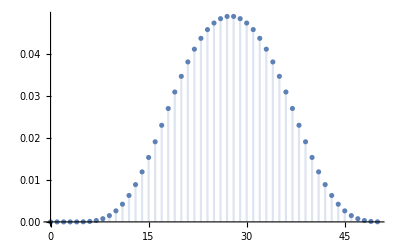

```mathematica
DiscretePlot[convoluteTCODI[x],{x,0,50}]
```

```mathematica
(*Probability function of sum*)
```

```mathematica
convoluteTCODI[x]
```

Piecewise[{{1/46080, x==5||x==50}, {1/9216, x==6||x==49}, {1/3072, x==7||x==48}, {7/9216, x==8||x==47}, {23/15360, x==9||x==46}, {121/46080, x==10||x==45}, {97/23040, x==11||x==44}, {29/4608, x==12||x==43}, {409/46080, x==13||x==42}, {61/5120, x==14||x==41}, {707/46080, x==15||x==40}, {293/15360, x==16||x==39}, {53/2304, x==17||x==38}, {311/11520, x==18||x==37}, {95/3072, x==19||x==36}, {1597/46080, x==20||x==35}, {39/1024, x==21||x==34}, {379/9216, x==22||x==33}, {1007/23040, x==23||x==32}, {211/4608, x==24||x==31}, {1091/23040, x==25||x==30}, {223/4608, x==26||x==29}, {1127/23040, 26<x<29}, {0, True}}]

```mathematica
(*Question No.2 Determine the exact probability of winning the Teddy prize.Also give a floating point answer.*)
```

```mathematica
RateOfWin=N[Sum[convoluteTCODI[x],{x,5,10}]+Sum[convoluteTCODI[x],{x,45,50}]]
```

0.0106771

```mathematica
(*Question No.3 Determine the exact probability of winning the Teddy prize.Also give a floating point answer.*)
```

```mathematica
NumberOfThrowToGetTeddy=1/RateOfWin
```

93.6585

```mathematica
InvestmentOfGetTeddy=NumberOfThrowToGetTeddy*2(*Euro*)
```

187.317

```mathematica
(*Question No.4 What's the probability of winning (at least one) Teddy if you play twenty times?*)
```

```mathematica
(*({{20}, {0}})=(20!)/((20-0)!0!)=(20!)/(20!1)=1 *)
1-(1-RateOfWin)^20
```

0.193208